Q2
Let’s start with a symbolic integration

```mathematica
Integrate[Sin[x]Exp[-x], x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
f[x_] := Sin[x]Exp[-x]
int[x] = Integrate[f[x], x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
-1/2 ⅇ^-x (Cos[x]+Sin[x])
D[int[x], x]
D[int[x], x]//Simplify
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

ⅇ^-x Sin[x]

Q4: Solve the following initial-value problem using both DSolve and NDSolve. Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

```mathematica
Clear
```

Clear

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

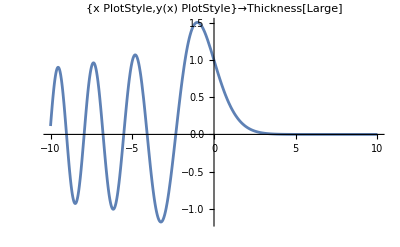

```mathematica
sol = DSolve[{y''[x]-x y[x]==0, y[0]==1, y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y[x],x]//FullSimplify

ySol[x_]=y[x]/. sol[[1]];
Plot[ySol[x],{x,-10,10},PlotRange->All,AxesLabel->{"x","y(x)"}PlotStyle->Thick]
```

```mathematica
f[x]//FullSimplify
```

{{y[x]→1-(3^(1/3) x Gamma[2/3])/Gamma[1/3]-x -xy[K[1]]K[1]10--xy[K[1]]K[1]1K[2]K[2]10+-xy[K[1]]K[1]1K[2]K[2]1x}}

```mathematica
sol=NDSolve[{y''[t]- t*y[t]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y,{t,0,60},AccuracyGoal->13,PrecisionGoal->13,MaxSteps->Infinity]
```

{{y→InterpolatingFunction[…]}}

NDSolve[{-ty[t]+y''[t]==0,y[0]==1,y'[0]==0},y,{t,0,60},Method→ImplicitRungeKutta,AccuracyGoal→13,PrecisionGoal→13,MaxSteps→∞]

{{y→InterpolatingFunction[…]}}